## Galois groups of quintics

```mathematica
GaloisGroup::usage = 
"GaloisGroup[quintic] computes the Galois group of the given
quintic.";
```

```mathematica
GaloisGroup::red = "The quintic is reducible.";
```

### Code

This can probably be done more efficiently by permuting coefficients and RootReducing the result

```mathematica
GaloisGroup::"usage"="GaloisGroup[quintic] computes the Galois group of the given quintic.";
GaloisGroup::"red"="The quintic is reducible.";
```

```mathematica
GaloisGroup[expr_]:=Module[{var},var=Union[Select[Level[expr,{-1}],Head[#1]===Symbol&]];If[Length[var]==1&&Exponent[expr,var⟦1⟧]==5,galois[expr,var⟦1⟧],Return[$Failed]]]
galois[expr_,var_]:=If[Exponent[expr,var]==5&&And@@(#1===Integer||#1===Rational&)/@Head/@CoefficientList[expr,var],Module[{factor},If[Head[factor=Factor[expr]]===Times&&Length[Complement[(Exponent[#1,var]&)/@List@@factor,{0,5}]]>0,Message[GaloisGroup::"red"];Select[(Irreducible[#1,var,Exponent[#1,var]]&)/@List@@factor,#1=!=Null&],If[Head[factor=Factor[expr]]===Power,Message[GaloisGroup::"red"];Table[SymmetricGroup[1],{i,Exponent[expr,var]}],{Irreducible[expr,var,Exponent[expr,var]]}]]],$Failed]
Irreducible[expr_,var_,n_]:=Module[{isfactorable,introot,roots},{isfactorable,introot,roots}=Resolvent[expr/Coefficient[expr,var,n],var];If[isfactorable,SolvableGroup[√Discriminant[expr,var],expr,var,introot,roots],If[IntegerQ[√Discriminant[expr,var]],AlternatingGroup[n],SymmetricGroup[n]],$Failed]]/;n==5
Irreducible[__]:=Null
Resolvent[expr_,var_]:=Module[{roots,integralroot,temp},roots=List@@NRoots[expr==0,var,20]/._==p_:>p;temp=Stabilizer/@Representatives[roots];integralroot=Position[Chop/@(Round[#1]-#1&)/@temp,_Integer];If[Length[integralroot]≥1,{True,Round[temp⟦integralroot⟦1,1⟧⟧],roots},{False,$Failed,$Failed}]]
Representatives[{x1_,x2_,x3_,x4_,x5_}]:={{x1,x2,x3,x4,x5},{x2,x1,x3,x4,x5},{x3,x2,x1,x4,x5},{x4,x2,x3,x1,x5},{x5,x2,x3,x4,x1},{x1,x5,x3,x4,x2}}
Stabilizer[{x1_,x2_,x3_,x4_,x5_}]:=x1^2 (x2 x5+x3 x4)+x2^2 (x1 x3+x4 x5)+x3^2 (x1 x5+x2 x4)+x4^2 (x1 x2+x3 x5)+x5^2 (x1 x4+x2 x3)
SolvableGroup[disc_,r__]:=If[!IntegerQ[disc],MetacyclicGroup[20],DihedralOrCyclic[r]]
DihedralOrCyclic[expr_,var_,introot_,roots_List]:=Module[{disc,p},Fnew[x1_,x2_,x3_,x4_,x5_]:=x1 x2^2+x2 x3^2+x3 x4^2+x4 x5^2+x5 x1^2;NewResolvent[{x1_,x2_,x3_,x4_,x5_}]:=(var-Fnew[x1,x2,x3,x4,x5]) (var-Fnew[x2,x1,x5,x4,x3]);p=Position[Round/@Stabilizer/@Representatives[roots],introot]⟦1,1⟧;disc=Discriminant[NewResolvent[Representatives[roots]⟦p⟧],var];disc=disc/.{e_Real:>Round[e],e_Complex:>Round[e]};If[disc==0,Return[SingularCase[expr,var,roots,5]]];If[IntegerQ[√disc],CyclicGroup[5],DihedralGroup[10]]]
SingularCase[expr_,var_,roots_,n_]:=Module[{newp,newroots,stabs,realr,p,disc},newp=Tschirnhaus[expr,var,n];newroots=newp/.({var->#1}&)/@roots;stabs=Stabilizer/@N[Representatives[newroots],32];realr=Select[Round[stabs],IntegerQ];If[Length[realr]==0,Return[$Failed]];p=Position[Round[stabs],First[realr]]⟦1,1⟧;disc=Discriminant[NewResolvent[Representatives[newroots]⟦p⟧],var];If[IntegerQ[√disc],CyclicGroup[5],DihedralGroup[10]]]
Tschirnhaus[expr_,var_,n_]:=Module[{z,randp,newp},randp=∑_(k=0)^(n-2) Random[Integer,{-1,0}] z^(n-k-2);newp=Resultant[expr/.var->z,var-randp,z];If[FreeQ[PolynomialGCD[newp,D[newp, var]],var],newp,Tschirnhaus[expr,var,n]]]
```

```mathematica
GaloisGroup[x^4+2x^2+1]
```

$Failed

## Galois Group

### Examples

```mathematica
{#,GaloisGroup[#]}&/@{x^5+20 x+32,x^5+x^4-4 x^3-3 x^2+3 x+1,x^5+x^4-12 x^3-21 x^2+x+5,x^5+2,x^5+20 x+16,x^5-5 x+12,x^5+15 x+12,x^5+5 x^3+10 x^2+5 x+4,x^5-33826005 x-4140303012}//TableForm//TraditionalForm
```

x^5+20 x+32 | DihedralGroup[10]
x^5+x^4-4 x^3-3 x^2+3 x+1 | CyclicGroup[5]
x^5+x^4-12 x^3-21 x^2+x+5 | CyclicGroup[5]
x^5+2 | MetacyclicGroup(20)
x^5+20 x+16 | AlternatingGroup[5]
x^5-5 x+12 | DihedralGroup[10]
x^5+15 x+12 | MetacyclicGroup(20)
x^5+5 x^3+10 x^2+5 x+4 | MetacyclicGroup(20)
x^5-33826005 x-4140303012 | DihedralGroup[10]

```mathematica
legend=Framed@TableForm[{
{Yellow,TraditionalForm["R"]},
{Red,TraditionalForm["S_n"]},
{Blue,TraditionalForm["M_n"]},
{Green,TraditionalForm["D_n"]},
{Purple,TraditionalForm["A_n"]},
{LightBlue,TraditionalForm["C_n"]}
},TableSpacing->{1,2}]
colorRule={
{}:>Yellow,
{SymmetricGroup[1],SymmetricGroup[1],SymmetricGroup[1],SymmetricGroup[1],SymmetricGroup[1]}:>Black,
{SymmetricGroup[n_]}:>Red,
{MetacyclicGroup[n_]}:>Blue,
{DihedralGroup[n_]}:>Green,
{AlternatingGroup[n_]}:>Purple,
{CyclicGroup[n_]}:>LightBlue
}
```

RGBColor[1, 1, 0] | R
RGBColor[1, 0, 0] | S_n
RGBColor[0, 0, 1] | M_n
RGBColor[0, 1, 0] | D_n
RGBColor[0.5, 0, 0.5] | A_n
RGBColor[0.87, 0.94, 1] | C_n

{{}:>Yellow,{SymmetricGroup[1],SymmetricGroup[1],SymmetricGroup[1],SymmetricGroup[1],SymmetricGroup[1]}:>Black,{SymmetricGroup[n_]}:>Red,{MetacyclicGroup[n_]}:>Blue,{DihedralGroup[n_]}:>Green,{AlternatingGroup[n_]}:>Purple,{CyclicGroup[n_]}:>LightBlue}

```mathematica
GaloisPlot[k_,dx_:.07]:=Module[{x,n},
Legended[
Graphics[Table[{GaloisGroup[x^5+p x+q],Rectangle[{p,q}+dx-.5,{p,q}+(1-dx)-.5]},{p,-k,k},{q,-k,k}] /.colorRule
,AspectRatio->Automatic,Frame->True,FrameLabel->TraditionalForm["x 的伽罗瓦群"]],
Placed[legend,Right]]
]
```

```mathematica
Off[GaloisGroup::"red"]
```

总运行时:  0.0184821

CPU 时间:  0.015625

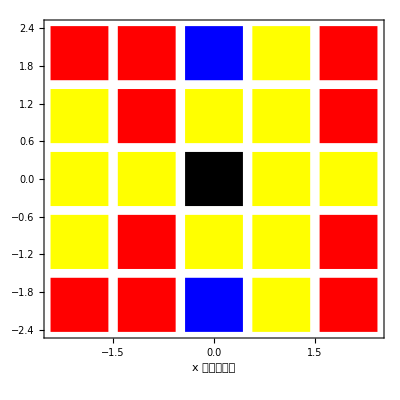

```mathematica
GaloisPlot[2]//TT
```

总运行时:  0.110519

CPU 时间:  0.125

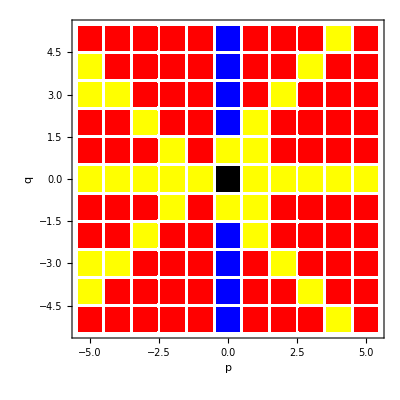

```mathematica
GaloisPlot[5]//TT
```

总运行时:  0.90644

CPU 时间:  0.890625

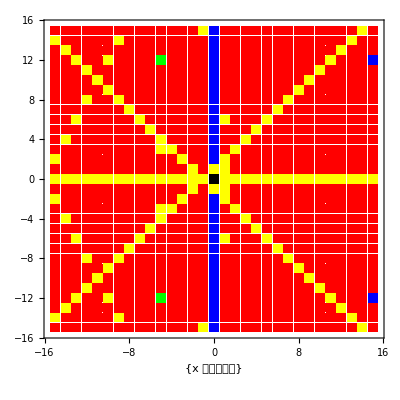

```mathematica
GaloisPlot[15]//TT
```

```mathematica
GaloisGroup[x^5-5x+12]
```

{DihedralGroup[10]}

```mathematica
Solve[x^5-5x+12==0,x]
```

{{x→Root[12-5 #1+#1^5&,1]},{x→Root[12-5 #1+#1^5&,2]},{x→Root[12-5 #1+#1^5&,3]},{x→Root[12-5 #1+#1^5&,4]},{x→Root[12-5 #1+#1^5&,5]}}

总运行时:  3.11073

CPU 时间:  3.10938

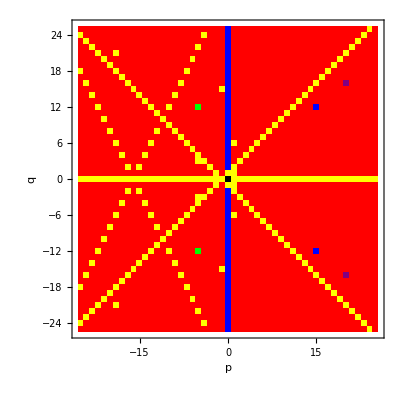

```mathematica
GaloisPlot[25]//TT
```

总运行时:  14.2074

CPU 时间:  14.2188

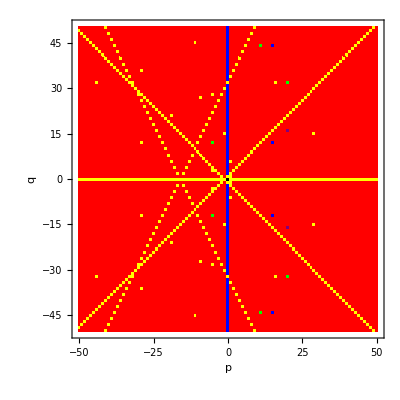

```mathematica
GaloisPlot[50]//TT
```

```mathematica
GaloisPlot[50]//Timing
```

{458.01 Second,⁃Graphics⁃}

```mathematica
GaloisGroup[x^5+x^4-3x^2+3x+1]
```

{SymmetricGroup[5]}